```mathematica
ClearAll["Global`*"]
```

```mathematica
{c0,c1,c2,c3,R,n}={-7.996631,0.136655,-13.015017,-0.627219,1.987204258 10^-3,1/2};
```

```mathematica
θ=1/(3.15 10^13);tf=250/θ;
```

```mathematica
tdata={0,43,44,100}3.15 10^13;
```

```mathematica
Tdata={283.,283.,403.,403.};
```

```mathematica
Tfun=Interpolation[Transpose[{tdata,Tdata}],InterpolationOrder->1];
```

```mathematica
thermalhist[t_,u_]=Tfun[t-u]
```

InterpolatingFunction[…][t-u]

```mathematica
k[u_]:=(c1 ⅇ^(-((-1+n) (c0+(c1 (c2-Log[u]))/(c3-Log[1/(R T)])))))/(u (-c3+Log[1/(R T)]))/.T->thermalhist[t,u];
```

```mathematica
rvals[t_]:=Max[0,1-((1-n) NIntegrate[k[u],{u,0,t},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->2])^(1/(1-n))]
```

```mathematica
rvals=Table[Max[0,1-((1-n) NIntegrate[k[u],{u,0,t},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->2])^(1/(1-n))],{t,0,tf,0.1tf}]
```

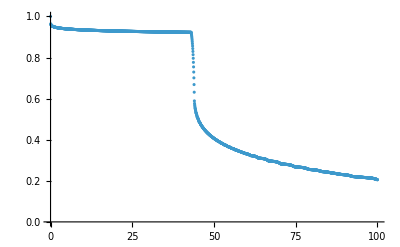

```mathematica
ListPlot[Table[{t/(3.15 10^13),rvals[t]},{t,0,100 3.15 10^13,0.05 3.15 10^13}]]
```